# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\My Drive\Doctorado\Quinto semestre\RESEARCH\Quantum maps\Codes

```mathematica
Get["QMB.wl"]
```

```mathematica
?IsingNNOpenHamiltonian
```

```mathematica
?DensityMatrix
```

```mathematica
?StateEvolution
```

```mathematica
?Dyad
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Choi & Kraus operators

## Setting parameters and global variables

```mathematica
{hx,hz,J,L}={1,0.5,1,4}
```

{1,0.5,1,4}

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Chop[Eigensystem[H]];
```

```mathematica
U[t_]:=MatrixExp[-I H t];
```

```mathematica
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
ψ0E=VectorFromKetInComputationalBasis[{0,0,0}]
```

{1,0,0,0,0,0,0,0}

```mathematica
(*Estado inicial 0⊗Subscript[ψ, 0E]*)
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
t=1;
```

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
```

```mathematica
A=Table[ρfSE=Dyad[
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigVals,eigVecs],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigVals,eigVecs]
];Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],{i,0,1},{j,0,1}];
```

```mathematica
superOperator=Transpose[Flatten[A,1]];
```

```mathematica
superOperator.{1,0,0,0}
```

{0.416537+0. ⅈ,-0.043617+0.221865 ⅈ,-0.043617-0.221865 ⅈ,0.583463+0. ⅈ}

```mathematica
Chop[superOperator//Eigensystem]
```

{{1.,-0.430388+0.482497 ⅈ,-0.430388-0.482497 ⅈ,0.421896},{{0.705828,-0.0517652+0.0134458 ⅈ,-0.0517652-0.0134458 ⅈ,0.704333},{-0.551884,-0.520734-0.0997931 ⅈ,0.235404+0.233048 ⅈ,0.551884},{-0.551884,0.235404-0.233048 ⅈ,-0.520734+0.0997931 ⅈ,0.551884},{-0.149707-0.0343956 ⅈ,0.690221,0.621006+0.301259 ⅈ,0.149707+0.0343956 ⅈ}}}

```mathematica
MatrixForm[CJmatrix=Reshuffle[superOperator]]
```

(0.416537+0. ⅈ | -0.141596+0.327207 ⅈ | -0.043617+0.221865 ⅈ | -0.139518+0.0877565 ⅈ
-0.141596-0.327207 ⅈ | 0.57638+0. ⅈ | 0.478217-0.229851 ⅈ | 0.00117016-0.201897 ⅈ
-0.043617-0.221865 ⅈ | 0.478217+0.229851 ⅈ | 0.583463+0. ⅈ | 0.141596-0.327207 ⅈ
-0.139518-0.0877565 ⅈ | 0.00117016+0.201897 ⅈ | 0.141596+0.327207 ⅈ | 0.42362+0. ⅈ)

```mathematica
CJmatrix//Eigensystem
```

{{1.41687,0.572384,0.00771374,0.00303186},{{-0.239843-0.246484 ⅈ,-0.103081+0.607101 ⅈ,-0.336286+0.527556 ⅈ,-0.333347+0. ⅈ},{-0.652862-0.0743702 ⅈ,-0.12046+0.218123 ⅈ,-0.0445672-0.204956 ⅈ,0.679822+0. ⅈ},{-0.108855-0.292249 ⅈ,0.613754+0.153681 ⅈ,-0.276724-0.59236 ⅈ,-0.273794+0. ⅈ},{0.563278-0.188204 ⅈ,0.363471+0.162145 ⅈ,-0.265671+0.257984 ⅈ,0.593092+0. ⅈ}}}

```mathematica
KrausOperators=Table[SparseArray[FromDigits[{r,#1,#2},2]+1->1,2^L].U[t=1].SparseArray[FromDigits[{s,0,0},2]+1->1,2^L],{r,0,1},{s,0,1}]&@@@Tuples[{0,1},2]
```

{{{-0.137116+0.286144 ⅈ,0.0106986-0.0941362 ⅈ},{0.0106986-0.0941362 ⅈ,-0.186767-0.173123 ⅈ}},{{0.290716-0.127252 ⅈ,0.0540951+0.105474 ⅈ},{0.0412091+0.118149 ⅈ,0.0963279+0.474584 ⅈ}},{{0.0106986-0.0941362 ⅈ,0.0822553+0.232989 ⅈ},{-0.104427+0.211869 ⅈ,-0.295262+0.161057 ⅈ}},{{-0.130854-0.225658 ⅈ,0.153393+0.187425 ⅈ},{-0.0475229+0.235465 ⅈ,-0.0570449+0.203084 ⅈ}}}

```mathematica
Chop@Sum[ConjugateTranspose[K].K,{K,KrausOperators}]
```

{{0.416537,0.0803088+0.105979 ⅈ},{0.0803088-0.105979 ⅈ,0.599713}}

```mathematica
ρ={1,x,y,z}.(Pauli/@Range[0,3])/2
```

{{(1+z)/2,1/2 (x-ⅈ y)},{1/2 (x+ⅈ y),(1-z)/2}}

```mathematica
ρFinal=Chop[FullSimplify[Total[#.ρ.ConjugateTranspose[#]&/@KrausOperators]]]
```

{{0.49663-0.142145 x+0.327167 y-0.0801301 z,(-0.0183884+0.00905543 ⅈ)+(0.170515-0.0686733 ⅈ) x+(0.158621+0.309188 ⅈ) y-(0.0245583-0.21293 ⅈ) z},{(-0.0183884-0.00905543 ⅈ)+(0.170515+0.0686733 ⅈ) x+(0.158621-0.309188 ⅈ) y-(0.0245583+0.21293 ⅈ) z,0.50337+0.142145 x-0.327167 y+0.0801301 z}}

```mathematica
BlochVectorFinal=Chop[FullSimplify[Tr[#.ρFinal]]]&/@(Pauli/@Range[0,3])[[2;;]]
```

{-0.0367768+0.34103 x+0.317242 y-0.0491167 z,-0.0181109+0.137347 x-0.618376 y-0.425859 z,-0.00674017-0.28429 x+0.654333 y-0.16026 z}

```mathematica
(BlochVectorFinal/.{x->#1,y->#2,z->#3})&@@{0,0,0}
```

{-0.0367768,-0.0181109,-0.00674017}

```mathematica
SeedRandom[23049];
ListPointPlot3D[(BlochVectorFinal/.{x->#1,y->#2,z->#3})&@@@RandomPoint[Sphere[{1,0,0},0.01],1000],Axes->True,PlotTheme->"Detailed",BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
RandomPoints=Table[{θ,ϕ}={RandomReal[{0,Pi/16}],RandomReal[{0,2Pi}]};
{Cos[ϕ]Sin[θ],Sin[θ]Sin[ϕ],Cos[θ]},100];
```

```mathematica
sphere=Graphics3D[{{Opacity[0.5],Sphere[]},Point[RandomPoints]},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Show[sphere,ListPointPlot3D[(BlochVectorFinal/.{x->#1,y->#2,z->#3})&@@@RandomPoints,Axes->True,PlotTheme->"Detailed"]]
```

-Graphics3D-

# All kraus operators

```mathematica
KrausOperators=Table[SparseArray[FromDigits[{r,#1,#2},2]+1->1,8].U[t=1].SparseArray[FromDigits[{s,0,0},2]+1->1,8],{r,0,1},{s,0,1}]&@@@Tuples[{0,1},2]
```

{{{0.147987+0.358403 ⅈ,0.191468-0.286941 ⅈ},{0.191468-0.286941 ⅈ,0.133578-0.149483 ⅈ}},{{0.191468-0.286941 ⅈ,-0.303873+0.25267 ⅈ},{-0.333272+0.255453 ⅈ,-0.453064-0.0176966 ⅈ}},{{-0.131625+0.0739518 ⅈ,-0.168937+0.294765 ⅈ},{-0.345416+0.0710369 ⅈ,0.0334327-0.374144 ⅈ}},{{-0.345416+0.0710369 ⅈ,0.0334327+0.430163 ⅈ},{-0.281707+0.290624 ⅈ,-0.0627265-0.180099 ⅈ}}}

```mathematica
KrausOperators//Dimensions
```

{4,2,2}

# Parametric evolution

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
(*Regular*)
{hx,hz,J,L}={1.,3.0,1,5};
```

```mathematica
(*caothic*)
{hx,hz,J,L}={1.,0.5,1,3};
```

```mathematica
Clear[H];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
Clear[U];
U[t_]:=MatrixExp[-I H t];
SeedRandom[32372];
(*Estado inicial de los qubits en el entorno Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
ψ0E=RandomChainProductState[L-1];
(*Estado inicial 0⊗Subscript[ψ, 0E]*)
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
```

```mathematica
(*Compute Subscript[ρ, 1](t) = Subscript[Tr, E](Ui⊗ψ0Ej⊗ψ0E U^†) *)
```

```mathematica
t=1000;
```

```mathematica
tlist=Range[0,10,0.5];
superoperators={};
Do[
superOperator=
Transpose[Flatten[Table[ρfSE=Dyad[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenval,eigenvec],
StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E],eigenval,eigenvec]];Flatten[MatrixPartialTrace[ρfSE,Range[2,L],2]],{i,0,1},{j,0,1}],1]];
AppendTo[superoperators,superOperator];
,{t,tlist}];
supereigen=Table[Eigensystem[i],{i,superoperators}];
rhos=Table[Chop[rho[supereigen[[i]][[2]][[1]]]],{i,Length[tlist]}];
stablepoints=Table[bloch[i],{i,rhos}];
```

```mathematica
CJmatrixs=Table[Reshuffle[i],{i,superoperators}];
choieigenvals=Table[Eigenvalues[i],{i,CJmatrixs}];
```

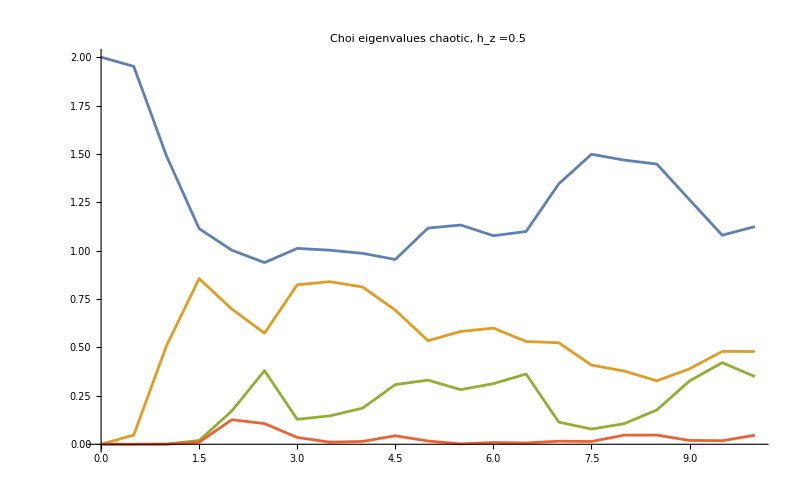

```mathematica
ListPlot[{Transpose[{tlist,choieigenvals[[All,1]]}],Transpose[{tlist,choieigenvals[[All,2]]}],Transpose[{tlist,choieigenvals[[All,3]]}],Transpose[{tlist,choieigenvals[[All,4]]}]},PlotRange->All,Joined->True,ImageSize->800,PlotLabel->Style["Choi eigenvalues chaotic, h_z ="<>ToString[hz],30,Black]]
```

```mathematica
superoperators//Dimensions
```

{21,4,4}

```mathematica
CJmatrixs=Table[Reshuffle[i],{i,superoperators}];
choisystem=Table[Transpose[Sort[Transpose[Eigensystem[i]]]],{i,CJmatrixs}];
```

```mathematica
choisystem//Dimensions
```

{21,2,4}

```mathematica
choisystem[[1]][[2]][[1]]
```

{0.+0. ⅈ,0.+0. ⅈ,-1.+6.245×10^-17 ⅈ,0.+0. ⅈ}